## Defining the polynomial and getting the roots

```mathematica
kmax=100
pol = ParallelTable[HypergeometricPFQ[{-n,a+n-1},{},-s/2]//Simplify,{n,0,100}]
```

100

```mathematica
rootsPlot=ComplexListPlot[N[(s/. Solve[#==0,s]&/@(pol[[80;;100;;2]]/.a->1))](**Table[k,{k,79,99,2}]*),AspectRatio->1]
```

$Aborted

## Finding the saddles

```mathematica
Clear[k]
phi=(1-1/k)Log[u]+Log[1+(u z)/(2k)]-u/k//FullSimplify;
Expand[u k(2k+u z) D[phi,u]//FullSimplify,u]
```

-2 k+2 k^2-2 k u-u z+2 k u z-u^2 z

```mathematica
Solve[D[(Series[phi,{k,Infinity,1}]//Normal),u]==0,u]
```

{{u→-(2 (-1+k))/(-2+z)}}

```mathematica
saddles=Solve[(D[phi,u]//FullSimplify)==0,u]//FullSimplify
```

{{u→(2 k (-1+z)-z+√(z^2-4 k z (1+z)+4 k^2 (1+z^2)))/(2 z)},{u→-(-2 k (-1+z)+z+√(z^2-4 k z (1+z)+4 k^2 (1+z^2)))/(2 z)}}

```mathematica
phiSaddles =Series[(phi/.saddles)//Simplify,{k,∞,0}]//PowerExpand//Normal//Simplify
```

{-1+1/z-(√(1+z^2))/z-Log[2]+Log[k]-Log[z]+Log[-1+z+√(1+z^2)]+Log[1+z+√(1+z^2)],-1+1/z+(√(1+z^2))/z-Log[2]+Log[k]-Log[z]+Log[-1+z-√(1+z^2)]+Log[1+z-√(1+z^2)]}

```mathematica
phiSaddles = phi/.saddles/.k->100//FullSimplify
```

{-(-200+199 z+√(40000+z (-400+39601 z)))/(200 z)+99/100 Log[(-200+199 z+√(40000+z (-400+39601 z)))/(2 z)]+Log[1/400 (200+199 z+√(40000+z (-400+39601 z)))],1/(200 z)(200+√(40000+z (-400+39601 z))+z (-199+200 Log[1/400 (200+199 z-√(40000+z (-400+39601 z)))]+198 Log[-(200-199 z+√(40000+z (-400+39601 z)))/(2 z)]))}

```mathematica
dom=ParallelTable[{x+I xx,If[Re[phiSaddles[[1]]-phiSaddles[[2]]/.z->x+I xx]>0,1,0]},{x,-2,0,0.01},{xx,-1.5,1.5,0.01}]
```

```mathematica
flat=Flatten[dom,1];
data={Re[#1],Im[#1],#2}&@@@flat;
Show[ListDensityPlot[data,InterpolationOrder->0,PlotLegends->Automatic,FrameLabel->{"Re[z]","Im[z]"}],rootsPlot]
```

-Graphics-

## Finding the saddles without 1/k term

```mathematica
phi=(1)Log[u]+Log[1+(u z)/(2k)]//FullSimplify
```

Log[u]+Log[1+(u z)/(2 k)]

```mathematica
saddles=Solve[(D[phi,u]//FullSimplify)==0,u]//FullSimplify
```

{{u→-k/z}}

```mathematica
phiSaddles = phi/.saddles/.k->100//FullSimplify
```

{Log[-50/z]}

## Defining Laguerre polynomials

```mathematica
kmax=100;
A=0.81;
polyLag = ParallelTable[LaguerreL[k,-A*k,k*s]//Simplify,{k,0,100}]
```

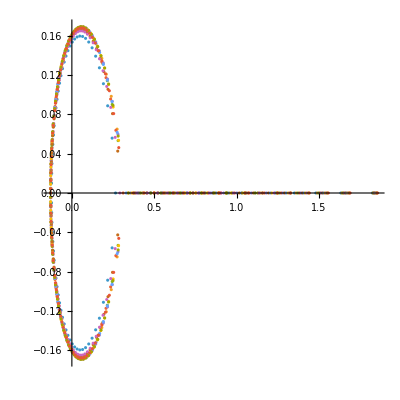

```mathematica
rootsPlotLag=ComplexListPlot[N[(s/. Solve[#==0,s]&/@(polyLag[[80;;100;;2]]))],AspectRatio->1]
```

## Finding the saddles

```mathematica
phiLag =-(z t)/(1-t)+A Log[1-t]-Log[t]-1/k Log[t(1-t)];
saddlesLag=Solve[(t(1-t)^2 k D[phiLag,t] //FullSimplify)==0,t]//FullSimplify
phiSaddlesLag = phiLag/.saddlesLag/.k->1000//FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→1/(10.5263+1. k)(7.89474+k (3.13158-2.63158 z)-0.0263158 √(10000.+k (-16200.-60000. z+k (6561.+z (-23800.+10000. z)))))},{t→1/(10.5263+1. k)(7.89474+k (3.13158-2.63158 z)+0.0263158 √(10000.+k (-16200.-60000. z+k (6561.+z (-23800.+10000. z)))))}}

{(z (-1.193+1. z+0.00001 √(6.54481×10^9+z (-2.386×10^10+1.×10^10 z))))/(-0.809+1. z+0.00001 √(6.54481×10^9+z (-2.386×10^10+1.×10^10 z)))-Log[3.10677-2.60417 z-0.0000260417 √(6.54481×10^9+z (-2.386×10^10+1.×10^10 z))]+0.81 Log[-2.10677+2.60417 z+0.0000260417 √(6.54481×10^9+z (-2.386×10^10+1.×10^10 z))]-1/1000 Log[-10.9837+0.000135769 √(6.54481×10^9+z (-2.386×10^10+1.×10^10 z))+z (29.758-13.5634 z-0.000135634 √(6.54481×10^9+z (-2.386×10^10+1.×10^10 z)))],0.4045+(0.5+2.22045×10^-16 z) z-5.×10^-6 √(6.54481×10^9+z (-2.386×10^10+1.×10^10 z))+0.81 Log[-2.10677+2.60417 z-0.0000260417 √(6.54481×10^9+z (-2.386×10^10+1.×10^10 z))]-1. Log[3.10677-2.60417 z+0.0000260417 √(6.54481×10^9+z (-2.386×10^10+1.×10^10 z))]-0.001 Log[-10.9837-0.000135769 √(6.54481×10^9+z (-2.386×10^10+1.×10^10 z))+z (29.758-13.5634 z+0.000135634 √(6.54481×10^9+z (-2.386×10^10+1.×10^10 z)))]}

```mathematica
domLag=ParallelTable[{x+I xx,If[Re[phiSaddlesLag[[1]]-phiSaddlesLag[[2]]/.z->x+I xx]>0,1,0]},{x,-0.2,1.5,0.005},{xx,-0.2,0.2,0.005}]
```

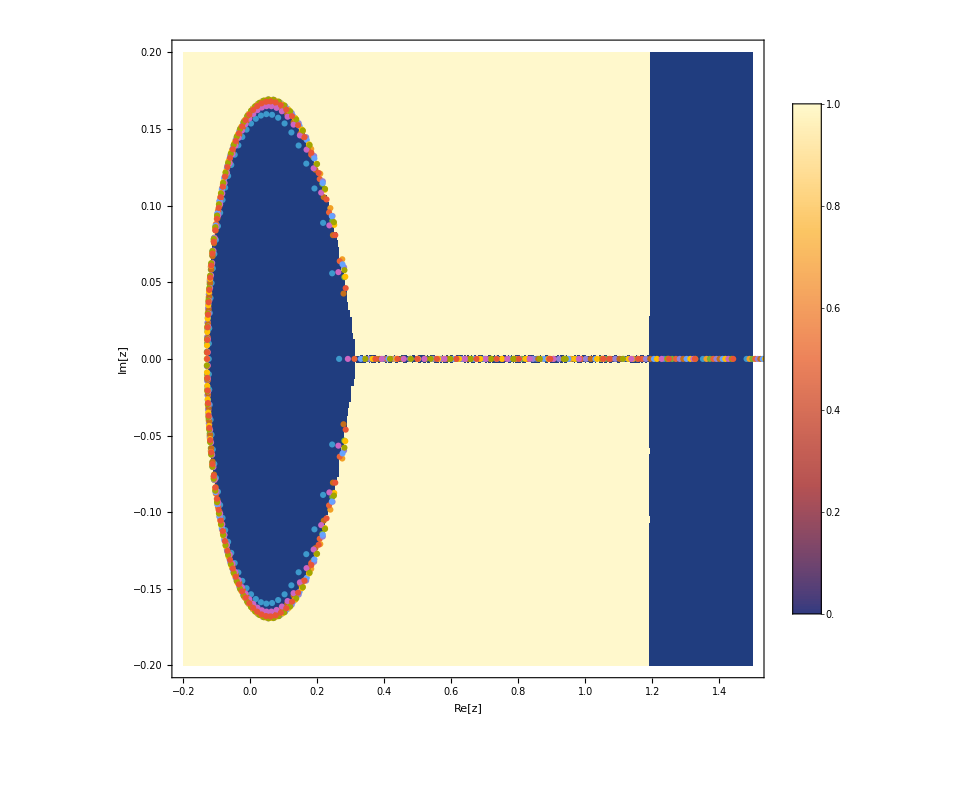

```mathematica
flat=Flatten[domLag,1];
data={Re[#1],Im[#1],#2}&@@@flat;
Show[ListDensityPlot[data,InterpolationOrder->0,PlotLegends->Automatic,FrameLabel->{"Re[z]","Im[z]"}],rootsPlotLag]
```